## Full Phase Diagram

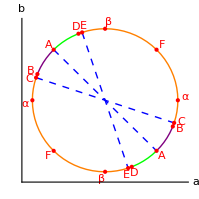

```mathematica
Angle1=ArcTan[1/3];
Angle2=ArcTan[0.3933];
Angle3=ArcTan[2.541];
Graphics[{{Orange,Thick,Circle[{0,0},1,{0,π/2}]},
{Orange,Thick,(*Dashed,*)Circle[{0,0},1,{-Angle1,0}]},
{Orange,Thick,(*Dashed,*)Circle[{0,0},1,{Angle1+π/2,π/2}]},
{Orange,Thick,Circle[{0,0},1,{π,(3π)/2}]},
{Orange,Thick,(*Dashed,*)Circle[{0,0},1,{π-Angle1,π}]},
{Orange,Thick,(*Dashed,*)Circle[{0,0},1,{3π/2,(3π)/2+Angle1}]},
{Green,Thick,Circle[{0,0},1,{π/2+Angle1,(3π)/4}]},
{Green,Thick,Circle[{0,0},1,{(3π)/2+Angle1,(7π)/4}]},
{Purple,Thick,Circle[{0,0},1,{(3π)/4,π-Angle1}]},

{Purple,Thick,Circle[{0,0},1,{(7π)/4,2π-Angle1}]},
{Thick,Dashed,Blue,Line[{{-Cos[Angle1+(3π)/2],-Sin[Angle1+(3π)/2]},{Cos[Angle1+(3π)/2],Sin[Angle1+(3π)/2]}}]},
{Thick,Dashed,Blue,Line[{{-Cos[Angle1],Sin[Angle1]},{Cos[Angle1],-Sin[Angle1]}}]},
{Thick,Dashed,Blue,Line[{{-Cos[π/4],Sin[π/4]},{Cos[π/4],-Sin[π/4]}}]},
{Red,PointSize[Medium],Point[{Cos[π/4],Sin[π/4]}],Inset[F,{1.1Cos[π/4],1.1Sin[π/4]}]},
{Red,PointSize[Medium],Point[{Cos[5π/4],Sin[5π/4]}],Inset[F,{1.1Cos[5π/4],1.1Sin[5π/4]}]},
{Red,PointSize[Medium],Point[{Cos[Angle1],-Sin[Angle1]}],Inset[C,{1.1Cos[Angle1],-1.1Sin[Angle1]+0.05}]},
{Red,PointSize[Medium],Point[{-Cos[Angle1],Sin[Angle1]}],Inset[C,{-1.1Cos[Angle1],1.1Sin[Angle1]-0.05}]},
{Red,PointSize[Medium],Point[{Cos[Angle2],-Sin[Angle2]}],Inset[B,{1.1Cos[Angle2],-1.1Sin[Angle2]}]},
{Red,PointSize[Medium],Point[{-Cos[Angle2],Sin[Angle2]}],Inset[B,{-1.1Cos[Angle2],1.1Sin[Angle2]}]},
{Red,PointSize[Medium],Point[{-Cos[π/4],Sin[π/4]}],Inset[A,{-1.1Cos[π/4],1.1Sin[π/4]}]},
{Red,PointSize[Medium],Point[{Cos[π/4],-Sin[π/4]}],Inset[A,{1.1Cos[π/4],-1.1Sin[π/4]}]},
{Red,PointSize[Medium],Point[{-Cos[Angle3],Sin[Angle3]}],Inset[D,{-1.1Cos[Angle3],1.1Sin[Angle3]}]},
{Red,PointSize[Medium],Point[{Cos[Angle3],-Sin[Angle3]}],Inset[D,{1.1Cos[Angle3],-1.1Sin[Angle3]}]},{Red,PointSize[Medium],Point[{Cos[Angle1+(3π)/2],Sin[Angle1+(3π)/2]}],Inset["E",{1.1Cos[Angle1+(3π)/2]-0.05,1.1Sin[Angle1+(3π)/2]}]},
{Red,PointSize[Medium],Point[{-Cos[Angle1+(3π)/2],-Sin[Angle1+(3π)/2]}],Inset["E",{-1.1Cos[Angle1+(3π)/2]+0.05,-1.1Sin[Angle1+(3π)/2]}]},
{Red,PointSize[Medium],Point[{1,0}],Inset["α",{1.1,0.05}]},{Red,PointSize[Medium],Point[{0,1}],Inset["β",{0.05,1.1}]},
{Red,PointSize[Medium],Point[{-1,0}],Inset["α",{-1.1,-0.05}]},{Red,PointSize[Medium],Point[{0,-1}],Inset["β",{-0.05,-1.1}]}
(*elemetns*)},Axes->True,AxesLabel->{a,b},Ticks->None]
```

## Diagram 1

```mathematica
data1={{-1.,-0.0004347655157338603},{-0.95,-0.0003537722378024605},{-0.9,-0.00023485459257851886},{-0.85,-0.00006821851219576333},{-0.8,0.00012956267182291474},{-0.75,0.0002763720486034134},{-0.7,0.0003741597884036451},{-0.6499999999999999,0.0004309458658956905},{-0.6,0.0004538466550318863},{-0.55,0.00044924044785566407},{-0.5,0.00042290856955782673},{-0.44999999999999996,0.0003801495498721172},{-0.3999999999999999,0.00032587919892887365},{-0.35,0.0002647155247432892},{-0.29999999999999993,0.00020105333917325423},{-0.25,0.00013912985193980515},{-0.19999999999999996,0.00008308440948530437},{-0.1499999999999999,0.00003701271473091541},{-0.09999999999999998,5.0183422666283135*^-6},{-0.04999999999999993,-8.739664061573104*^-6},{0.,-1.7724614407549463*^-17},{0.050000000000000044,0.00003564636157058268},{0.10000000000000009,0.00010280205214349648},{0.15000000000000013,0.0002063081582120499},{0.20000000000000018,0.0003512909788327928},{0.25,0.0005432115062530664},{0.30000000000000004,0.0007879145711880853},{0.3500000000000001,0.0010916841357498219},{0.40000000000000013,0.0014612983432871146},{0.4500000000000002,0.0019040941763956536},{0.5,0.0024280315635730404},{0.55,0.00304177038001253},{0.6000000000000001,0.0036447132491935885},{0.6500000000000001,0.004101571267831065},{0.7000000000000002,0.004446716619648046},{0.75,0.004705785197488224},{0.8,0.004897403011315932},{0.8500000000000001,0.005035393176009401},{0.9000000000000001,0.005130209750134656},{0.9500000000000002,0.005189887554398288},{1.,0.0052206953551680695}};
```

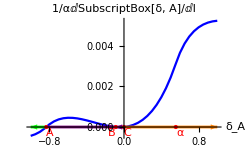

```mathematica
ListLinePlot[data1,PlotStyle->Blue,Epilog->{{AbsoluteThickness[2],Green,Arrowheads[{{0.05,0.8}}],Arrow[{{-5/6,0},{-1,0}}]},
{AbsoluteThickness[2],Purple,Arrowheads[{{0.05,0.5}}],Arrow[{{-5/6,0},{-0.0883,0}}]},
{AbsoluteThickness[2],Purple,Arrowheads[{{0.03,0.9}}],Arrow[{{0,0},{-0.0883,0}}]},
{AbsoluteThickness[2],Orange,Arrowheads[{{0.05,0.5}}],Arrow[{{0,0},{1,0}}]},
{PointSize[Medium],Red,Point[{0,0}],Inset["C",{0.04,-0.0003}]},{PointSize[Medium],Red,Point[{-0.0883,0}],Inset["B",{-0.13,-0.0003}]},
{PointSize[Medium],Red,Point[{-5/6,0}],Inset["A",{-0.8,-0.0003}]},{PointSize[Medium],Red,Point[{5/9,0}],Inset["α",{0.6,-0.0003}]}(*epilogend*)},

AxesLabel->{"δ_A","1/αⅆSubscriptBox[δ, A]/ⅆl"}]
```

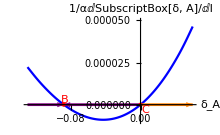

```mathematica
data2={{-0.13,0.000022294286315899768},{-0.12000000000000001,0.000015862435856805242},{-0.11,0.000010092545467299324},{-0.1,5.0183422666309156*^-6},{-0.09,6.730526114239778*^-7},{-0.08,-2.9092145067729624*^-6},{-0.07,-5.694770674297914*^-6},{-0.06,-7.64862047944936*^-6},{-0.05,-8.739664061574947*^-6},{-0.04000000000000001,-8.930239972841278*^-6},{-0.03,-8.186713718838024*^-6},{-0.020000000000000004,-6.473977371314148*^-6},{-0.010000000000000009,-3.7569255033723407*^-6},{0.,-1.7724614407549463*^-17},{0.010000000000000009,4.8325363632263185*^-6},{0.01999999999999999,0.000010776799794492726},{0.03,0.00001786933076253558},{0.04000000000000001,0.000026146707349348477},{0.04999999999999999,0.000035646361570580514},{0.06,0.000046405702745989344}};
ListLinePlot[data2,PlotStyle->Blue,Epilog->{{AbsoluteThickness[2],Purple,Arrowheads[{{0.05,0.5}}],Arrow[{{0,0},{-0.0883,0}}]},
{AbsoluteThickness[2],Orange,Arrowheads[{{0.05,0.5}}],Arrow[{{0,0},{0.06,0}}]},
{AbsoluteThickness[2],Purple,Arrowheads[{{0.05,0.5}}],Arrow[{{-0.13,0},{-0.0883,0}}]},{PointSize[Medium],Red,Point[{0,0}],Inset["C",{0.006,-0.000003}]},{PointSize[Medium],Red,Point[{-0.0883,0}],Inset["B",{-0.087,0.000003}]}
(*elementsend*)},
InterpolationOrder->2,PlotRange->{{-0.13,0.06},{-0.00001,0.00005}},AxesLabel->{"δ_A","1/αⅆSubscriptBox[δ, A]/ⅆl"}]
```

## Diagram 2

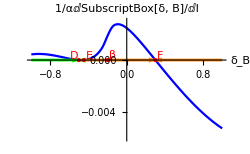

```mathematica
data3={{-1.,0.00043476551573387416},{-0.95,0.00046317324029724986},{-0.9,0.0004641147015763229},{-0.85,0.0004405520573396819},{-0.8,0.00039595990207133905},{-0.75,0.0003344956516828611},{-0.7,0.00026116144533102487},{-0.6499999999999999,0.00018212321127850963},{-0.6,0.00010508289513704028},{-0.55,0.00003985336450560567},{-0.5,-8.16229374126301*^-7},{-0.44999999999999996,3.4523630482174994*^-11},{-0.3999999999999999,0.00006528796707646126},{-0.35,0.00022705085802056987},{-0.29999999999999993,0.0005310211998992669},{-0.25,0.001044473808825011},{-0.19999999999999996,0.0018695449799890833},{-0.1499999999999999,0.0025405687139255367},{-0.09999999999999998,0.002735811410245148},{-0.04999999999999993,0.0026661901201291416},{0.,0.0024405735568092295},{0.050000000000000044,0.002120271615659677},{0.10000000000000009,0.0017419874546322402},{0.15000000000000013,0.001328574040799242},{0.20000000000000018,0.0008946178408381312},{0.25,0.0004496296118700746},{0.30000000000000004,8.673617379884035*^-19},{0.3500000000000001,-0.00044971113044006087},{0.40000000000000013,-0.0008960455134147619},{0.4500000000000002,-0.0013361735573229686},{0.5,-0.0017676537743197916},{0.55,-0.0021883285537799835},{0.6000000000000001,-0.0025962467337757138},{0.6500000000000001,-0.0029896512753046778},{0.7000000000000002,-0.0033669520530254966},{0.75,-0.0037267088701232534},{0.8,-0.004067622099751493},{0.8500000000000001,-0.004388509839683689},{0.9000000000000001,-0.004688295124778386},{0.9500000000000002,-0.004965991088324613},{1.,-0.005220695355168078}};
ListLinePlot[data3,PlotStyle->Blue,InterpolationOrder->2,PlotRange->{{-1,1},{-0.006,0.003}},Epilog->{{AbsoluteThickness[2],Green,Arrowheads[{{0.05,0.5}}],Arrow[{{-1,0},{-0.502,0}}]},
{AbsoluteThickness[2],Green,Arrowheads[{{0.02,0.9}}],Arrow[{{-0.450,0},{-0.502,0}}]},
{AbsoluteThickness[2],Orange,Arrowheads[{{0.05,0.5}}],Arrow[{{-0.450,0},{0.3,0}}]},
{AbsoluteThickness[2],Orange,Arrowheads[{{0.05,0.5}}],Arrow[{{1,0},{0.3,0}}]},
{PointSize[Medium],Red,Point[{0.3,0}],Inset["F",{0.35,0.0003}]},{PointSize[Medium],Red,Point[{-0.450,0}],Inset["E",{-0.39,0.0003}]},
{PointSize[Medium],Red,Point[{-0.502,0}],Inset["D",{-0.55,+0.0003}]},{PointSize[Medium],Red,Point[{-1/5,0}],Inset["β",{-0.15,+0.0004}]}
(*endofelements*)},AxesLabel->{"δ_B","1/αⅆSubscriptBox[δ, B]/ⅆl"}]
```

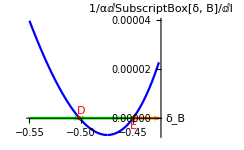

```mathematica
data4={{-0.55,0.00003985336450560567},{-0.545,0.00003443980590388078},{-0.54,0.00002928094834905512},{-0.535,0.000024397924777192978},{-0.53,0.000019800767601605915},{-0.525,0.00001550669437363865},{-0.52,0.000011532969743380944},{-0.515,7.895996463886182*^-6},{-0.51,4.613338483809223*^-6},{-0.505,1.7026369137102676*^-6},{-0.5,-8.16229374126301*^-7},{-0.49500000000000005,-2.925678095245729*^-6},{-0.49000000000000005,-4.605398752919113*^-6},{-0.48500000000000004,-5.8351890064988615*^-6},{-0.48000000000000004,-6.5943264168019655*^-6},{-0.47500000000000003,-6.8605340139277216*^-6},{-0.47000000000000003,-6.612849006272861*^-6},{-0.465,-5.826592443249415*^-6},{-0.4600000000000001,-4.4783779856918254*^-6},{-0.45500000000000007,-2.545158553432167*^-6},{-0.45000000000000007,3.452362354328109*^-11},{-0.44500000000000006,3.1844860888200627*^-6},{-0.44000000000000006,7.030335986315042*^-6},{-0.43500000000000005,0.000011571090335029538},{-0.43000000000000005,0.000016829375071815075},{-0.42500000000000004,0.00002284137721174622}};
ListLinePlot[data4,PlotStyle->Blue,InterpolationOrder->2,AxesLabel->{"δ_B","1/αⅆSubscriptBox[δ, B]/ⅆl"},Epilog->{{AbsoluteThickness[2],Green,Arrowheads[{{0.05,0.5}}],Arrow[{{-0.55,0},{-0.502,0}}]},{AbsoluteThickness[2],Green,Arrowheads[{{0.05,0.5}}],Arrow[{{-0.450,0},{-0.502,0}}]},
{AbsoluteThickness[2],Orange,Arrowheads[{{0.05,0.5}}],Arrow[{{-0.450,0},{-0.425,0}}]},
{PointSize[Medium],Red,Point[{-0.450,0}],Inset["E",{-0.45,-0.000003}]},
{PointSize[Medium],Red,Point[{-0.502,0}],Inset["D",{-0.50,0.000003}]}
(*endofelements*)}]
```

## Polarization diagram

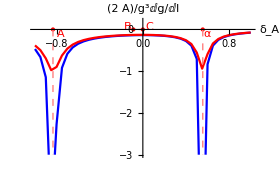

```mathematica
data5={{-1.,-0.46824601386212783},{-0.95,-0.6611648610498377},{-0.9,-1.143596458623985},{-0.85,-4.520498449370337},{-0.8,-2.269416761188397},{-0.75,-0.9191771804405929},{-0.7,-0.5820149540480883},{-0.6499999999999999,-0.42905914299919257},{-0.6,-0.34196710293447036},{-0.55,-0.28586859882737004},{-0.5,-0.24688263121027806},{-0.44999999999999996,-0.21838054403845128},{-0.3999999999999999,-0.1968140376375196},{-0.35,-0.1801239482788514},{-0.29999999999999993,-0.16704802372135333},{-0.25,-0.15678462909784135},{-0.19999999999999996,-0.148807756376298},{-0.1499999999999999,-0.14279301383958173},{-0.09999999999999998,-0.13854337779643325},{-0.04999999999999993,-0.13597251869934857},{0.,-0.13509491166529417},{0.050000000000000044,-0.13603378771081318},{0.10000000000000009,-0.13905013623905085},{0.15000000000000013,-0.14460389541133806},{0.20000000000000018,-0.15347494399116937},{0.25,-0.16700923048550084},{0.30000000000000004,-0.18765876607519313},{0.3500000000000001,-0.22031505890837222},{0.40000000000000013,-0.27621356547740206},{0.4500000000000002,-0.387958389534352},{0.5,-0.705616623177633},{0.55,-6.782789473342962},{0.6000000000000001,-0.832222310389164},{0.6500000000000001,-0.3858317050554258},{0.7000000000000002,-0.24886060558019676},{0.75,-0.18258183239569875},{0.8,-0.1435960534775264},{0.8500000000000001,-0.11798399964667759},{0.9000000000000001,-0.09991117586574941},{0.9500000000000002,-0.08650261902368456},{1.,-0.07617805806580487}};
data6={{-1.,-0.38202954935622363},{-0.95,-0.49560472297258346},{-0.9,-0.692098919988848},{-0.85,-0.9750089609769315},{-0.8,-0.897100341172346},{-0.75,-0.6242358588307886},{-0.7,-0.4593056383596703},{-0.6499999999999999,-0.3617438838554989},{-0.6,-0.2989040668043926},{-0.55,-0.25551134814286863},{-0.5,-0.2239869829952717},{-0.44999999999999996,-0.20023781440146088},{-0.3999999999999999,-0.18188785569031868},{-0.35,-0.16748020327847504},{-0.29999999999999993,-0.15608517234811442},{-0.25,-0.14709470934695776},{-0.19999999999999996,-0.1401089887394878},{-0.1499999999999999,-0.13487202597621545},{-0.09999999999999998,-0.13123554588337355},{-0.04999999999999993,-0.12914111264732037},{0.,-0.12861608872765276},{0.050000000000000044,-0.12978331991362063},{0.10000000000000009,-0.1328880877124604},{0.15000000000000013,-0.13835256192955972},{0.20000000000000018,-0.1468804641430308},{0.25,-0.15966418962363327},{0.30000000000000004,-0.17882385215600943},{0.3500000000000001,-0.20843699703134327},{0.40000000000000013,-0.2573166929701606},{0.4500000000000002,-0.3480858176089071},{0.5,-0.5536289524701636},{0.55,-0.9386667584130514},{0.6000000000000001,-0.5896601087791442},{0.6500000000000001,-0.33510821038938376},{0.7000000000000002,-0.22740942954699842},{0.75,-0.17038279984965315},{0.8,-0.13545226954605552},{0.8500000000000001,-0.11198290274891154},{0.9000000000000001,-0.09518805088971033},{0.9500000000000002,-0.0826097494880868},{1.,-0.07286007562906008}};
ListLinePlot[{data5,data6},PlotStyle->{Blue,Red},AxesLabel->{"δ_A","(2  A)/g^3ⅆg/ⅆl"},AxesOrigin->{0,0},InterpolationOrder->1,PlotRange->{{-1,1},{-3,0.2}},Epilog->{{PointSize[Medium],Red,Point[{-5/6,0}],Inset["A",{-0.76,-0.1}]},{Thick,Dashed,Pink,Line[{{-5/6,0},{-5/6,-3}}]},
{PointSize[Medium],Red,Point[{5/9,0}],Inset["α",{0.6,-0.1}]},{PointSize[Medium],Red,Point[{0,0}],Inset["C",{0.06,0.05}]},{PointSize[Medium],Red,Point[{-0.0883,0}],Inset["B",{-0.14,0.05}]},{Thick,Dashed,Pink,Line[{{5/9,0},{5/9,-3}}]}}]
```

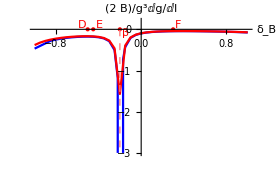

```mathematica
data7={{-1.,-0.4682460138621449},{-0.85,-0.2786742067592013},{-0.8,-0.2480245624880005},{-0.75,-0.22484719334499736},{-0.7,-0.20714300991260048},{-0.6499999999999999,-0.19376827785253478},{-0.6,-0.1841558400633836},{-0.55,-0.17822406971491045},{-0.5,-0.17644166919053883},{-0.44999999999999996,-0.18012654873489792},{-0.3999999999999999,-0.19230148879573866},{-0.35,-0.22034786900878706},{-0.29999999999999993,-0.2867066876014438},{-0.25,-0.5039149253175312},{-0.22,-1.1749607420688175},{-0.19999999999999996,-10^204},{-0.17,-0.7305834641676603},{-0.1499999999999999,-0.43116159318328034},{-0.09999999999999998,-0.20786277734923064},{-0.04999999999999993,-0.1345598157727488},{0.,-0.0987548271223245},{0.050000000000000044,-0.078022950354633},{0.10000000000000009,-0.064945751797904},{0.15000000000000013,-0.05637339672835166},{0.20000000000000018,-0.05073434707039377},{0.25,-0.04713959960028351},{0.30000000000000004,-0.04503163724029968},{0.3500000000000001,-0.04403335856994461},{0.40000000000000013,-0.04387867593204691},{0.4500000000000002,-0.04437768611172591},{0.5,-0.04539655748088121},{0.55,-0.04684406004188382},{0.6000000000000001,-0.04866169903828804},{0.6500000000000001,-0.05081636202712734},{0.7000000000000002,-0.053295038903336145},{0.75,-0.05610119736536227},{0.8,-0.059252895882295896},{0.8500000000000001,-0.06278191549371057},{0.9000000000000001,-0.06673434773283145},{0.9500000000000002,-0.07117249315915954},{1.,-0.0761780580658049}};
data8={{-1.,-0.38202954935622346},{-0.95,-0.32386188121889403},{-0.9,-0.28167479401945594},{-0.85,-0.2500475179637092},{-0.8,-0.22576476339599322},{-0.75,-0.20686771359675787},{-0.7,-0.19215842655149984},{-0.6499999999999999,-0.18094577504971013},{-0.6,-0.17293007867736407},{-0.55,-0.16818749106521608},{-0.5,-0.16726718534182164},{-0.44999999999999996,-0.1714881190671665},{-0.3999999999999999,-0.1837387584715363},{-0.35,-0.21088597889890787},{-0.29999999999999993,-0.27312746728640686},{-0.25,-0.46336402119490067},{-0.19999999999999996,-1.5693896044005105},{-0.1499999999999999,-0.3944078381016288},{-0.09999999999999998,-0.19753833116887698},{-0.04999999999999993,-0.12881297943036177},{0.,-0.09463431710843359},{0.050000000000000044,-0.07469469600680326},{0.10000000000000009,-0.06207558059562276},{0.15000000000000013,-0.053795153006756795},{0.20000000000000018,-0.04835174827854989},{0.25,-0.04489032764420615},{0.30000000000000004,-0.04287202964565021},{0.3500000000000001,-0.04193098468032422},{0.40000000000000013,-0.04180825144117788},{0.4500000000000002,-0.04231850770053305},{0.5,-0.043330718921275324},{0.55,-0.04475509394013784},{0.6000000000000001,-0.04653348578374272},{0.6500000000000001,-0.04863218264419017},{0.7000000000000002,-0.051036655839952594},{0.75,-0.05374796699808447},{0.8,-0.05678058989613202},{0.8500000000000001,-0.060161450861557164},{0.9000000000000001,-0.06393006692929568},{0.9500000000000002,-0.06813976364910822},{1.,-0.07286007562906016}};
ListLinePlot[{data7,data8},PlotRange->{{-1,1},{-3,0.2}},PlotStyle->{Blue,Red},AxesLabel->{"δ_B","(2  B)/g^3ⅆg/ⅆl"},InterpolationOrder->1,Epilog->{{PointSize[Medium],Red,Point[{-1/5,0}],Inset["β",{-0.15,-0.1}]},{PointSize[Medium],Red,Point[{0.3,0}],Inset["F",{0.35,0.1}]},{PointSize[Medium],Red,Point[{-0.450,0}],Inset["E",{-0.39,0.1}]},
{PointSize[Medium],Red,Point[{-0.502,0}],Inset["D",{-0.55,+0.1}]},{Thick,Dashed,Pink,Line[{{-1/5,0},{-1/5,-3}}]} }]
```

## Others

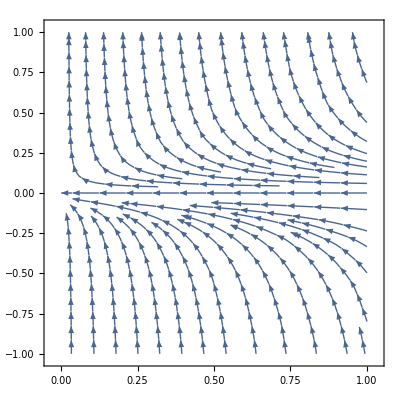

```mathematica
StreamPlot[{-x^3/y^2,10 x^2},{x,0,1},{y,-1,1}]
```

```mathematica
H[a_,b_,kx_,ky_,kz_]:=ConjugateTranspose[({{ⅈ, 0, 0, 0}, {0, 0, -ⅈ, 0}, {0, 0, 0, -ⅈ}, {0, ⅈ, 0, 0}})].Simplify[{{a kz,0,-(a+3b)/4(kx+I ky),(√3)/4(a-b)(kx-I ky)},{0,b kz,(√3)/4(a-b)(kx-I ky),-(3a+b)/4(kx+I ky)},{-(a+3b)/4(kx-I ky),(√3)/4(a-b)(kx+I ky),-a kz,0},{(√3)/4(a-b)(kx+I ky),-(3a+b)/4(kx-I ky),0,-b kz}}].({{ⅈ, 0, 0, 0}, {0, 0, -ⅈ, 0}, {0, 0, 0, -ⅈ}, {0, ⅈ, 0, 0}})
```

```mathematica
Eigenvalues[H[0,-1,kx,ky,kz]]
```

{-1/2 √(2 kx^2+2 ky^2+2 kz^2-√(4 kx^4-kx^2 ky^2+4 ky^4-kx^2 kz^2-ky^2 kz^2+4 kz^4)),1/2 √(2 kx^2+2 ky^2+2 kz^2-√(4 kx^4-kx^2 ky^2+4 ky^4-kx^2 kz^2-ky^2 kz^2+4 kz^4)),-1/2 √(2 kx^2+2 ky^2+2 kz^2+√(4 kx^4-kx^2 ky^2+4 ky^4-kx^2 kz^2-ky^2 kz^2+4 kz^4)),1/2 √(2 kx^2+2 ky^2+2 kz^2+√(4 kx^4-kx^2 ky^2+4 ky^4-kx^2 kz^2-ky^2 kz^2+4 kz^4))}

```mathematica
ContourPlot3D[1/2 √(2 kx^2+2 ky^2+2 kz^2-√(4 kx^4-kx^2 ky^2+4 ky^4-kx^2 kz^2-ky^2 kz^2+4 kz^4))==0.1,{kx,-1,1},{ky,-1,1},{kz,-1,1},Ticks->None,PlotLabel->"tan φ=-∞"]
```

-Graphics3D-

```mathematica
Graphics[{{Orange,Thick,Circle[{0,0},1,{0,π/2}]},
{Purple,Thick,Circle[{0,0},1,{7π/4,2π}]},
{Green, Thick, Circle[{0,0},1,{3π/2,7π/4}]},
{Orange, Thick, Circle[{0,0},1,{π,3π/2}]},
{Green, Thick, Circle[{0,0},1,{π/2,3π/4}]},
{Purple, Thick, Circle[{0,0},1,{3π/4,π}]},
{Red,PointSize[Medium],Point[{Cos[π/4],-Sin[π/4]}],Inset["A",{1.2Cos[π/4],-1.2Sin[π/4]}]},

{Red,PointSize[Medium],Point[{-Cos[π/4],Sin[π/4]}],Inset["A",{-1.2Cos[π/4],1.2Sin[π/4]}]},
{Red,PointSize[Medium],Point[{1,0}],Inset["α",{1.2,-0.05}]},{Red,PointSize[Medium],Point[{0,-1}],Inset["β",{-0.05,-1.2}]},{Red,PointSize[Medium],Point[{-1,0}],Inset["α",{-1.2,-0.05}]},{Red,PointSize[Medium],Point[{0,1}],Inset["β",{-0.05,1.2}]}
},Axes->True,AxesLabel->{"a","b"},Ticks->None]
```

-Graphics-

```mathematica
Show[SphericalPlot3D[{1,-1},{θ,0.02,ArcTan[√2]-0.02},{ϕ,0,2π},PlotStyle->{Orange,Orange},PlotRange->All,Ticks->None,AxesLabel->{"k_x","k_y","k_z"},Mesh->None],SphericalPlot3D[{1,-1},{θ,ArcTan[√2]+0.02,π/2-0.02},{ϕ,0,2π},PlotStyle->{Orange,Orange},PlotRange->All,Ticks->None,Mesh->None]]
```

-Graphics3D-